# QCD calculation: Webber et al. Sec. 7

-Graphics-

## Two-jet cross sections (Only QCD; mass ignored) : Ellis-Stirling-Webber Sec.7.5

-Graphics-

### Initialization

```mathematica
Exit[];
```

```mathematica
$Language="English";
<<FeynArts`
<<FormCalc`
```

FeynArts 3.9

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 2 Dec 14

FormCalc 8.4

by Thomas Hahn

last revised 5 Nov 14

$CharacterEncoding::utf8: The byte sequence {160} could not be interpreted as a character in the UTF-8 character encoding.

### Create Topology (and also ignore helicities)

```mathematica
topologies=CreateTopologies[0,2->2];
_Hel=0;
```

### q q' -> q q'

loading generic model file /Users/misho/Documents/Mathematica/lib/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts/Models/SMQCD.mod

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counter terms of order 1

> 6 counter terms of order 2

classes model {SMQCD} initialized

Excluding 0 Generic, 6 Classes, and 6 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 6 Classes, and 6 Particles fields

in total: 1 Classes insertion

> Top. 1: 1 diagram

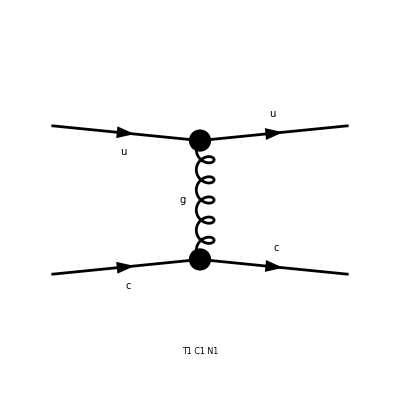

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

```mathematica
diag=InsertFields[topologies,{F[3,{1}],F[3,{2}]}->{F[3,{1}],F[3,{2}]},InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]}];
Paint[diag];
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
```

```mathematica
SquaredME[amp]//.HelicityME[amp]//FullSimplify
```

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

1/9 Alfas2 π^2 (4 MC2^2+4 MU2^2+T^2+(S-U)^2+2 MC2 (4 MU2-S+T-U)-2 MU2 (S-T+U)) Den[T,0]^2 (9 Mat[SUN1,SUN1]-3 (Mat[SUN1,SUN2]+Mat[SUN2,SUN1])+Mat[SUN2,SUN2])

```mathematica
%//.Abbr[]
```

1/9 Alfas2 π^2 (4 MC2^2+4 MU2^2+T^2+(S-U)^2+2 MC2 (4 MU2-S+T-U)-2 MU2 (S-T+U)) Den[T,0]^2 (9 Mat[SUNT[Col1,Col4] SUNT[Col2,Col3],SUNT[Col1,Col4] SUNT[Col2,Col3]]-3 (Mat[SUNT[Col1,Col4] SUNT[Col2,Col3],SUNT[Col1,Col3] SUNT[Col2,Col4]]+Mat[SUNT[Col1,Col3] SUNT[Col2,Col4],SUNT[Col1,Col4] SUNT[Col2,Col3]])+Mat[SUNT[Col1,Col3] SUNT[Col2,Col4],SUNT[Col1,Col3] SUNT[Col2,Col4]])

```mathematica
SquaredME[amp]//.HelicityME[amp]//.ColourME[amp]//FullSimplify
```

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

8 Alfas2 π^2 (4 MC2^2+4 MU2^2+T^2+(S-U)^2+2 MC2 (4 MU2-S+T-U)-2 MU2 (S-T+U)) Den[T,0]^2

```mathematica
%//.Subexpr[]//.{Alfas2->(gs^2/(4π))^2,MC2->0,MU2->0,Den[a_,b_]:>1/(a-b)}
```

(gs^4 (T^2+(S-U)^2))/(2 T^2)

```mathematica
FullSimplify[gs^4 4/9(S^2+U^2)/T^2//.U->-S-T]
```

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

ggggg..................
HelicityME takes AVARAGE, and ColourME takes SUM!!!!!!!!!!!!!!

#### LESSON

×2 for each FINAL fermion

DIVIDE by INITIAL colour factor

```mathematica
FullSimplify[(SquaredME[amp]//.HelicityME[amp]//.ColourME[amp])*2^2/3^2//.{Alfas2->(gs^2/(4π))^2,MC->0,MU->0,MC2->0,MU2->0,Den[a_,b_]:>1/(a-b)}]
FullSimplify[gs^4 4/9(S^2+U^2)/T^2//.U->-S-T]
```

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

(2 gs^4 (T^2+(S-U)^2))/(9 T^2)

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

### q q' -> q q' (Again)

```mathematica
diag=InsertFields[topologies,{F[3,{1}],F[3,{2}]}->{F[3,{1}],F[3,{2}]},InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]}];
Paint[diag];
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
FullSimplify[(SquaredME[amp]//.HelicityME[amp]//.ColourME[amp])*2^2/3^2//.Subexpr[]//.{Alfas2->(gs^2/(4π))^2,MC->0,MU->0,MC2->0,MU2->0,Den[a_,b_]:>1/(a-b)}//.U->-S-T]
FullSimplify[gs^4 4/9(S^2+U^2)/T^2//.U->-S-T]
```

Excluding 0 Generic, 6 Classes, and 6 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 6 Classes, and 6 Particles fields

in total: 1 Classes insertion

> Top. 1: 1 diagram

-Graphics-

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM... running FORM...

ok

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

ok

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

(4 gs^4 (2 S^2+2 S T+T^2))/(9 T^2)

### g q -> g q

Excluding 0 Generic, 6 Classes, and 6 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

Restoring 0 Generic, 6 Classes, and 6 Particles fields

in total: 3 Classes insertions

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

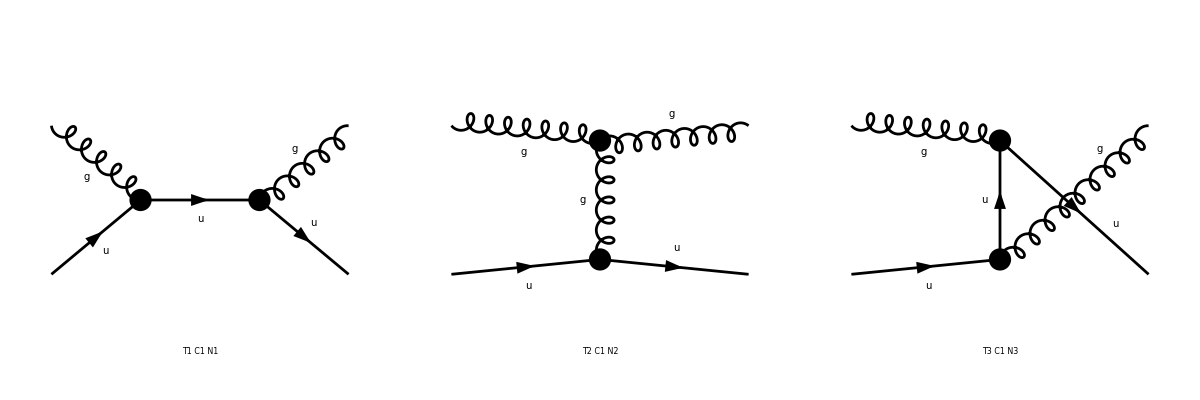

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM... running FORM...

ok

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

ok

1/12 (128/3 Alfas2 (Abb18+2 MU2 Pair1 Pair7) π^2 Den[S,MU2]^2+32/3 Abb20 Alfas2 Pair1 π^2 Den[S,MU2] (4 Den[S,MU2]+8 Den[T,0])+32/3 Abb10 Alfas2 Pair2 Pair7 π^2 Den[S,MU2] (4 Den[S,MU2]+8 Den[T,0])-32/3 Abb16 Alfas2 π^2 Pair1^* Den[S,MU2] (4 Den[S,MU2]+8 Den[T,0])+32/3 Abb1 Alfas2 Pair1 π^2 Pair2^* Den[S,MU2] (4 Den[S,MU2]+8 Den[T,0])+8/3 Alfas2 (-Abb7-2 MU2) Pair1 π^2 Pair1^* (4 Den[S,MU2]+8 Den[T,0])^2+8/3 Abb6 Alfas2 Pair2 π^2 Pair1^* (4 Den[S,MU2]+8 Den[T,0])^2+8/3 Abb5 Alfas2 Pair1 π^2 Pair2^* (4 Den[S,MU2]+8 Den[T,0])^2-8/3 Alfas2 Pair2 π^2 (MU2-S) (MU2-U) Pair2^* (4 Den[S,MU2]+8 Den[T,0])^2-256/3 Abb22 Alfas2 π^2 Den[S,MU2] (Pair3 Den[S,MU2]+Pair4 Den[T,0])+64/3 Alfas2 (Abb21+2 MU2 Pair14) π^2 Pair1^* (4 Den[S,MU2]+8 Den[T,0]) (Pair3 Den[S,MU2]+Pair4 Den[T,0])-64/3 Alfas2 (Abb13+2 MU2 Pair1) π^2 Pair2^* (4 Den[S,MU2]+8 Den[T,0]) (Pair3 Den[S,MU2]+Pair4 Den[T,0])+256/3 Abb17 Alfas2 π^2 Den[S,MU2] (Pair3^* Den[S,MU2]+Pair4^* Den[T,0])+64/3 Alfas2 Pair1 (Abb19+2 MU2 Pair15) π^2 (4 Den[S,MU2]+8 Den[T,0]) (Pair3^* Den[S,MU2]+Pair4^* Den[T,0])-64/3 Alfas2 Pair2 (Abb15+2 MU2 Pair7) π^2 (4 Den[S,MU2]+8 Den[T,0]) (Pair3^* Den[S,MU2]+Pair4^* Den[T,0])+512/3 Alfas2 (-Abb12-2 MU2) π^2 (Pair3 Den[S,MU2]+Pair4 Den[T,0]) (Pair3^* Den[S,MU2]+Pair4^* Den[T,0])-32/3 Alfas2 (Abb18+2 MU2 Pair1 Pair7) π^2 Den[S,MU2] Den[U,MU2]-4/3 Abb20 Alfas2 Pair1 π^2 (4 Den[S,MU2]+8 Den[T,0]) Den[U,MU2]-4/3 Abb10 Alfas2 Pair2 Pair7 π^2 (4 Den[S,MU2]+8 Den[T,0]) Den[U,MU2]+4/3 Abb16 Alfas2 π^2 Pair1^* (4 Den[S,MU2]+8 Den[T,0]) Den[U,MU2]-4/3 Abb1 Alfas2 Pair1 π^2 Pair2^* (4 Den[S,MU2]+8 Den[T,0]) Den[U,MU2]+32/3 Abb22 Alfas2 π^2 (Pair3 Den[S,MU2]+Pair4 Den[T,0]) Den[U,MU2]-32/3 Abb17 Alfas2 π^2 (Pair3^* Den[S,MU2]+Pair4^* Den[T,0]) Den[U,MU2]+128/3 Alfas2 (Abb18+2 MU2 Pair1 Pair7) π^2 Den[U,MU2]^2+4/3 Abb20 Alfas2 Pair1 π^2 Den[S,MU2] (8 Den[T,0]+4 Den[U,MU2])+4/3 Abb10 Alfas2 Pair2 Pair7 π^2 Den[S,MU2] (8 Den[T,0]+4 Den[U,MU2])-4/3 Abb16 Alfas2 π^2 Pair1^* Den[S,MU2] (8 Den[T,0]+4 Den[U,MU2])+4/3 Abb1 Alfas2 Pair1 π^2 Pair2^* Den[S,MU2] (8 Den[T,0]+4 Den[U,MU2])+2/3 Alfas2 (-Abb7-2 MU2) Pair1 π^2 Pair1^* (4 Den[S,MU2]+8 Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])+2/3 Abb6 Alfas2 Pair2 π^2 Pair1^* (4 Den[S,MU2]+8 Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])+2/3 Abb5 Alfas2 Pair1 π^2 Pair2^* (4 Den[S,MU2]+8 Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])-2/3 Alfas2 Pair2 π^2 (MU2-S) (MU2-U) Pair2^* (4 Den[S,MU2]+8 Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])+8/3 Alfas2 (Abb21+2 MU2 Pair14) π^2 Pair1^* (Pair3 Den[S,MU2]+Pair4 Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])-8/3 Alfas2 (Abb13+2 MU2 Pair1) π^2 Pair2^* (Pair3 Den[S,MU2]+Pair4 Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])+8/3 Alfas2 Pair1 (Abb19+2 MU2 Pair15) π^2 (Pair3^* Den[S,MU2]+Pair4^* Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])-8/3 Alfas2 Pair2 (Abb15+2 MU2 Pair7) π^2 (Pair3^* Den[S,MU2]+Pair4^* Den[T,0]) (8 Den[T,0]+4 Den[U,MU2])-32/3 Abb20 Alfas2 Pair1 π^2 Den[U,MU2] (8 Den[T,0]+4 Den[U,MU2])-32/3 Abb10 Alfas2 Pair2 Pair7 π^2 Den[U,MU2] (8 Den[T,0]+4 Den[U,MU2])+32/3 Abb16 Alfas2 π^2 Pair1^* Den[U,MU2] (8 Den[T,0]+4 Den[U,MU2])-32/3 Abb1 Alfas2 Pair1 π^2 Pair2^* Den[U,MU2] (8 Den[T,0]+4 Den[U,MU2])+8/3 Alfas2 (-Abb7-2 MU2) Pair1 π^2 Pair1^* (8 Den[T,0]+4 Den[U,MU2])^2+8/3 Abb6 Alfas2 Pair2 π^2 Pair1^* (8 Den[T,0]+4 Den[U,MU2])^2+8/3 Abb5 Alfas2 Pair1 π^2 Pair2^* (8 Den[T,0]+4 Den[U,MU2])^2-8/3 Alfas2 Pair2 π^2 (MU2-S) (MU2-U) Pair2^* (8 Den[T,0]+4 Den[U,MU2])^2-4/3 Abb22 Alfas2 π^2 Den[S,MU2] (8 Pair4 Den[T,0]-8 Pair5 Den[U,MU2])+1/3 Alfas2 (Abb21+2 MU2 Pair14) π^2 Pair1^* (4 Den[S,MU2]+8 Den[T,0]) (8 Pair4 Den[T,0]-8 Pair5 Den[U,MU2])-1/3 Alfas2 (Abb13+2 MU2 Pair1) π^2 Pair2^* (4 Den[S,MU2]+8 Den[T,0]) (8 Pair4 Den[T,0]-8 Pair5 Den[U,MU2])+8/3 Alfas2 (-Abb12-2 MU2) π^2 (Pair3^* Den[S,MU2]+Pair4^* Den[T,0]) (8 Pair4 Den[T,0]-8 Pair5 Den[U,MU2])+32/3 Abb22 Alfas2 π^2 Den[U,MU2] (8 Pair4 Den[T,0]-8 Pair5 Den[U,MU2])+8/3 Alfas2 (Abb21+2 MU2 Pair14) π^2 Pair1^* (8 Den[T,0]+4 Den[U,MU2]) (8 Pair4 Den[T,0]-8 Pair5 Den[U,MU2])-8/3 Alfas2 (Abb13+2 MU2 Pair1) π^2 Pair2^* (8 Den[T,0]+4 Den[U,MU2]) (8 Pair4 Den[T,0]-8 Pair5 Den[U,MU2])+4/3 Abb17 Alfas2 π^2 Den[S,MU2] (8 Pair4^* Den[T,0]-8 Pair5^* Den[U,MU2])+1/3 Alfas2 Pair1 (Abb19+2 MU2 Pair15) π^2 (4 Den[S,MU2]+8 Den[T,0]) (8 Pair4^* Den[T,0]-8 Pair5^* Den[U,MU2])-1/3 Alfas2 Pair2 (Abb15+2 MU2 Pair7) π^2 (4 Den[S,MU2]+8 Den[T,0]) (8 Pair4^* Den[T,0]-8 Pair5^* Den[U,MU2])+8/3 Alfas2 (-Abb12-2 MU2) π^2 (Pair3 Den[S,MU2]+Pair4 Den[T,0]) (8 Pair4^* Den[T,0]-8 Pair5^* Den[U,MU2])-32/3 Abb17 Alfas2 π^2 Den[U,MU2] (8 Pair4^* Den[T,0]-8 Pair5^* Den[U,MU2])+8/3 Alfas2 Pair1 (Abb19+2 MU2 Pair15) π^2 (8 Den[T,0]+4 Den[U,MU2]) (8 Pair4^* Den[T,0]-8 Pair5^* Den[U,MU2])-8/3 Alfas2 Pair2 (Abb15+2 MU2 Pair7) π^2 (8 Den[T,0]+4 Den[U,MU2]) (8 Pair4^* Den[T,0]-8 Pair5^* Den[U,MU2])+8/3 Alfas2 (-Abb12-2 MU2) π^2 (8 Pair4 Den[T,0]-8 Pair5 Den[U,MU2]) (8 Pair4^* Den[T,0]-8 Pair5^* Den[U,MU2]))

```mathematica
diag=InsertFields[topologies,{V[5],F[3,{1}]}->{V[5],F[3,{1}]},InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]}];
Paint[diag];
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
matrix=(SquaredME[amp]//.HelicityME[amp]//.ColourME[amp])*2/(3×8)
```

```mathematica
MyResult=1/2 PolarizationSum[matrix,GaugeTerms->False]//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),MU->0,MU2->0,Alfas2->(gs^2/(4π))^2}//FullSimplify
WebberResult=gs^4(-4/9(S^2+U^2)/(S U)+(U^2+S^2)/T^2)//FullSimplify
```

preparing FORM code in /Users/misho/fc-pol-1.frm

running FORM...

ok

(gs^4 (T (36 S^3+3 S^2 T-19 S T^2-2 T^3)-5 T^2 (4 S+T) U+(-72 S^2+17 T^2) U^2+36 T U^3))/(36 S T^2 U)

1/9 gs^4 (9/T^2-4/(S U)) (S^2+U^2)

```mathematica
FullSimplify[MyResult==WebberResult,Assumptions->{S+T+U==0}]
```

True

We used GaugeTerms→False, because we know the diagram set is gauge-independent.
This is, but, a very bad habit, and not recommended.
I recommend you to check the gauge-independence in advance.

```mathematica
MyResultWithGaugeTerms=1/2 PolarizationSum[matrix,GaugeTerms->True]//.Subexpr[]//.Abbr[]//.Den[p2_,m2_]:>1/(p2-m2)
```

preparing FORM code in /Users/misho/fc-pol-1.frm

running FORM...

ok

1/2 Alfas2 π^2 ((16 (1))/T^2-(32 (-(2 MU2^3 Pair[1])/(Pair[1] 1)+4))/(9 (-MU2+U)^2)+(32 (1))/(9 (1)^2)+(4 (1/1+3+1))/((-MU2+S) T)+((4 (1))/(9 (-MU2+S))+(4 (1))/T)/(-MU2+U))
 |  |  |  |

```mathematica
MyResultWithGaugeTerms//.MU2->(S+T+U)/2//Simplify
```

(4 Alfas2 π^2 (Pair[eta[1],k[1]] (T (63 S^5-40 T^5+S^4 (242 T-225 U)+9 T^4 U+142 T^3 U^2-136 T^2 U^3-166 T U^4+63 U^5+S^3 (28 T^2-564 T U+234 U^2)+S^2 (-522 T^3-540 T^2 U+236 T U^2+18 U^3)+S (-283 T^4+648 T^2 U^2+252 T U^3-153 U^4)) Pair[eta[3],k[1]]-2 T^2 (-71 S^4+33 T^4-19 T^3 U-159 T^2 U^2+51 T U^3+158 U^4+3 S^3 (8 T+61 U)+S^2 (262 T^2+323 T U+5 U^2)+S (136 T^3-39 T^2 U-398 T U^2-275 U^3)) Pair[eta[3],k[2]]+18 S^6 Pair[eta[3],k[3]]+63 S^5 T Pair[eta[3],k[3]]+22 S^4 T^2 Pair[eta[3],k[3]]+304 S^3 T^3 Pair[eta[3],k[3]]+1036 S^2 T^4 Pair[eta[3],k[3]]+593 S T^5 Pair[eta[3],k[3]]+12 T^6 Pair[eta[3],k[3]]-108 S^5 U Pair[eta[3],k[3]]-207 S^4 T U Pair[eta[3],k[3]]-20 S^3 T^2 U Pair[eta[3],k[3]]+860 S^2 T^3 U Pair[eta[3],k[3]]+164 S T^4 U Pair[eta[3],k[3]]-425 T^5 U Pair[eta[3],k[3]]+270 S^4 U^2 Pair[eta[3],k[3]]+126 S^3 T U^2 Pair[eta[3],k[3]]+384 S^2 T^2 U^2 Pair[eta[3],k[3]]-832 S T^3 U^2 Pair[eta[3],k[3]]-1080 T^4 U^2 Pair[eta[3],k[3]]-360 S^3 U^3 Pair[eta[3],k[3]]+234 S^2 T U^3 Pair[eta[3],k[3]]-796 S T^2 U^3 Pair[eta[3],k[3]]-332 T^3 U^3 Pair[eta[3],k[3]]+270 S^2 U^4 Pair[eta[3],k[3]]-333 S T U^4 Pair[eta[3],k[3]]+410 T^2 U^4 Pair[eta[3],k[3]]-108 S U^5 Pair[eta[3],k[3]]+117 T U^5 Pair[eta[3],k[3]]+18 U^6 Pair[eta[3],k[3]]-46 S^4 T^2 Pair[eta[3],k[4]]+44 S^3 T^3 Pair[eta[3],k[4]]+392 S^2 T^4 Pair[eta[3],k[4]]+276 S T^5 Pair[eta[3],k[4]]+102 T^6 Pair[eta[3],k[4]]+208 S^3 T^2 U Pair[eta[3],k[4]]+460 S^2 T^3 U Pair[eta[3],k[4]]+88 S T^4 U Pair[eta[3],k[4]]+28 T^5 U Pair[eta[3],k[4]]+36 S^3 T U^2 Pair[eta[3],k[4]]-60 S^2 T^2 U^2 Pair[eta[3],k[4]]-576 S T^3 U^2 Pair[eta[3],k[4]]-256 T^4 U^2 Pair[eta[3],k[4]]-108 S^2 T U^3 Pair[eta[3],k[4]]-320 S T^2 U^3 Pair[eta[3],k[4]]+72 T^3 U^3 Pair[eta[3],k[4]]+108 S T U^4 Pair[eta[3],k[4]]+218 T^2 U^4 Pair[eta[3],k[4]]-36 T U^5 Pair[eta[3],k[4]])-T (Pair[eta[1],k[4]] ((63 S^5+S^4 (124 T-225 U)+2 S^3 (10 T^2-75 T U+117 U^2)+S^2 (-6 T^3+38 T^2 U+42 T U^2+18 U^3)+(T+U)^2 (10 T^3-61 T^2 U-12 T U^2+63 U^3)+S (45 T^4-14 T^3 U-36 T^2 U^2-130 T U^3-153 U^4)) Pair[eta[3],k[1]]+4 T (6 S^4-4 T^4-2 S^3 (7 T-6 U)-3 T^3 U+13 T^2 U^2+3 T U^3-9 U^4-S^2 (2 T^2+17 T U+51 U^2)+2 S (7 T^3+8 T^2 U+14 T U^2+21 U^3)) Pair[eta[3],k[2]]-9 S^5 Pair[eta[3],k[3]]-90 S^4 T Pair[eta[3],k[3]]+40 S^3 T^2 Pair[eta[3],k[3]]+298 S^2 T^3 Pair[eta[3],k[3]]+97 S T^4 Pair[eta[3],k[3]]-80 T^5 Pair[eta[3],k[3]]+9 S^4 U Pair[eta[3],k[3]]-90 S^3 T U Pair[eta[3],k[3]]+554 S^2 T^2 U Pair[eta[3],k[3]]+174 S T^3 U Pair[eta[3],k[3]]-543 T^4 U Pair[eta[3],k[3]]-18 S^3 U^2 Pair[eta[3],k[3]]+350 S^2 T U^2 Pair[eta[3],k[3]]+124 S T^2 U^2 Pair[eta[3],k[3]]-1036 T^3 U^2 Pair[eta[3],k[3]]+90 S^2 U^3 Pair[eta[3],k[3]]-70 S T U^3 Pair[eta[3],k[3]]-718 T^2 U^3 Pair[eta[3],k[3]]-117 S U^4 Pair[eta[3],k[3]]-100 T U^4 Pair[eta[3],k[3]]+45 U^5 Pair[eta[3],k[3]]+72 S^4 T Pair[eta[3],k[4]]+52 S^3 T^2 Pair[eta[3],k[4]]-124 S^2 T^3 Pair[eta[3],k[4]]-52 S T^4 Pair[eta[3],k[4]]+52 T^5 Pair[eta[3],k[4]]-206 S^3 T U Pair[eta[3],k[4]]-118 S^2 T^2 U Pair[eta[3],k[4]]+102 S T^3 U Pair[eta[3],k[4]]+78 T^4 U Pair[eta[3],k[4]]+36 S^3 U^2 Pair[eta[3],k[4]]+134 S^2 T U^2 Pair[eta[3],k[4]]+108 S T^2 U^2 Pair[eta[3],k[4]]+10 T^3 U^2 Pair[eta[3],k[4]]-108 S^2 U^3 Pair[eta[3],k[4]]+62 S T U^3 Pair[eta[3],k[4]]-42 T^2 U^3 Pair[eta[3],k[4]]+108 S U^4 Pair[eta[3],k[4]]-62 T U^4 Pair[eta[3],k[4]]-36 U^5 Pair[eta[3],k[4]])+Pair[eta[1],k[3]] ((27 S^5+S^4 (157 T-90 U)+53 T (T^2-U^2)^2+2 S^3 (57 T^2-97 T U+54 U^2)-2 S^2 (41 T^3+59 T^2 U+15 T U^2+27 U^3)+S (-13 T^4-14 T^3 U+4 T^2 U^2+14 T U^3+9 U^4)) Pair[eta[3],k[1]]+(-36 S^5+27 T^5+29 T^4 U+70 T^3 U^2+34 T^2 U^3-97 T U^4-63 U^5+3 S^4 (19 T+45 U)+2 S^3 (19 T^2+2 T U-63 U^2)-4 S^2 (21 T^3+56 T^2 U+69 T U^2+18 U^3)+S (-2 T^4+64 T^3 U+152 T^2 U^2+312 T U^3+162 U^4)) Pair[eta[3],k[2]]+27 S^5 Pair[eta[3],k[3]]-123 S^4 T Pair[eta[3],k[3]]-54 S^3 T^2 Pair[eta[3],k[3]]+374 S^2 T^3 Pair[eta[3],k[3]]+155 S T^4 Pair[eta[3],k[3]]-123 T^5 Pair[eta[3],k[3]]-126 S^4 U Pair[eta[3],k[3]]-46 S^3 T U Pair[eta[3],k[3]]+710 S^2 T^2 U Pair[eta[3],k[3]]+174 S T^3 U Pair[eta[3],k[3]]-584 T^4 U Pair[eta[3],k[3]]+108 S^3 U^2 Pair[eta[3],k[3]]+422 S^2 T U^2 Pair[eta[3],k[3]]+84 S T^2 U^2 Pair[eta[3],k[3]]-1054 T^3 U^2 Pair[eta[3],k[3]]+162 S^2 U^3 Pair[eta[3],k[3]]-214 S T U^3 Pair[eta[3],k[3]]-740 T^2 U^3 Pair[eta[3],k[3]]-279 S U^4 Pair[eta[3],k[3]]-39 T U^4 Pair[eta[3],k[3]]+108 U^5 Pair[eta[3],k[3]]+36 S^5 Pair[eta[3],k[4]]+39 S^4 T Pair[eta[3],k[4]]-42 S^3 T^2 Pair[eta[3],k[4]]-48 S^2 T^3 Pair[eta[3],k[4]]+6 S T^4 Pair[eta[3],k[4]]+9 T^5 Pair[eta[3],k[4]]-135 S^4 U Pair[eta[3],k[4]]-162 S^3 T U Pair[eta[3],k[4]]+38 S^2 T^2 U Pair[eta[3],k[4]]+102 S T^3 U Pair[eta[3],k[4]]+37 T^4 U Pair[eta[3],k[4]]+162 S^3 U^2 Pair[eta[3],k[4]]+206 S^2 T U^2 Pair[eta[3],k[4]]+68 S T^2 U^2 Pair[eta[3],k[4]]-8 T^3 U^2 Pair[eta[3],k[4]]-36 S^2 U^3 Pair[eta[3],k[4]]-82 S T U^3 Pair[eta[3],k[4]]-64 T^2 U^3 Pair[eta[3],k[4]]-54 S U^4 Pair[eta[3],k[4]]-T U^4 Pair[eta[3],k[4]]+27 U^5 Pair[eta[3],k[4]])+Pair[eta[1],k[2]] ((-63 S^5+66 T^5-3 S^4 (38 T-63 U)-205 T^4 U-134 T^3 U^2+76 T^2 U^3-124 T U^4-63 U^5+2 S^3 (37 T^2+85 T U-63 U^2)+2 S^2 (152 T^3+60 T^2 U-61 T U^2-63 U^3)+S (245 T^4-66 T^3 U-270 T^2 U^2+190 T U^3+189 U^4)) Pair[eta[3],k[1]]-2 (S^4 (7 T+18 U)+S^3 (-75 T^2+14 T U-54 U^2)-S^2 (153 T^3+113 T^2 U+62 T U^2-54 U^3)+S (-117 T^4+72 T^3 U+209 T^2 U^2+54 T U^3-18 U^4)+T (-46 T^4+117 T^3 U+155 T^2 U^2-21 T U^3-13 U^4)) Pair[eta[3],k[2]]+9 S^5 Pair[eta[3],k[3]]+80 S^4 T Pair[eta[3],k[3]]-134 S^3 T^2 Pair[eta[3],k[3]]-596 S^2 T^3 Pair[eta[3],k[3]]-387 S T^4 Pair[eta[3],k[3]]+4 T^5 Pair[eta[3],k[3]]+27 S^4 U Pair[eta[3],k[3]]+70 S^3 T U Pair[eta[3],k[3]]-712 S^2 T^2 U Pair[eta[3],k[3]]-94 S T^3 U Pair[eta[3],k[3]]+789 T^4 U Pair[eta[3],k[3]]-90 S^3 U^2 Pair[eta[3],k[3]]-270 S^2 T U^2 Pair[eta[3],k[3]]+182 S T^2 U^2 Pair[eta[3],k[3]]+1294 T^3 U^2 Pair[eta[3],k[3]]+18 S^2 U^3 Pair[eta[3],k[3]]+10 S T U^3 Pair[eta[3],k[3]]+664 T^2 U^3 Pair[eta[3],k[3]]+81 S U^4 Pair[eta[3],k[3]]+110 T U^4 Pair[eta[3],k[3]]-45 U^5 Pair[eta[3],k[3]]-82 S^4 T Pair[eta[3],k[4]]-146 S^3 T^2 Pair[eta[3],k[4]]-174 S^2 T^3 Pair[eta[3],k[4]]-238 S T^4 Pair[eta[3],k[4]]-128 T^5 Pair[eta[3],k[4]]+36 S^4 U Pair[eta[3],k[4]]+186 S^3 T U Pair[eta[3],k[4]]-40 S^2 T^2 U Pair[eta[3],k[4]]-22 S T^3 U Pair[eta[3],k[4]]+168 T^4 U Pair[eta[3],k[4]]-144 S^3 U^2 Pair[eta[3],k[4]]-54 S^2 T U^2 Pair[eta[3],k[4]]+198 S T^2 U^2 Pair[eta[3],k[4]]+248 T^3 U^2 Pair[eta[3],k[4]]+216 S^2 U^3 Pair[eta[3],k[4]]-122 S T U^3 Pair[eta[3],k[4]]-12 T^2 U^3 Pair[eta[3],k[4]]-144 S U^4 Pair[eta[3],k[4]]+72 T U^4 Pair[eta[3],k[4]]+36 U^5 Pair[eta[3],k[4]]))))/(9 T^2 (S+T-U)^2 (-S+T+U)^2 Pair[eta[1],k[1]] Pair[eta[3],k[3]])

It seems that this amplitude depends on “eta”, and thus gauge-dependent. However, note that, in this 2→2 process, k[1]+k[2]==k[3]+k[4]. Therefore...

```mathematica
%//.{Pair[eta_,k[2]]:>Pair[eta,k[3]]+Pair[eta,k[4]]-Pair[eta,k[1]]}//Simplify
```

1/(9 T^2 (S+T-U)^2 (-S+T+U)^2)8 Alfas2 π^2 (9 S^6+21 T^6+18 S^5 (2 T-3 U)+84 T^5 U+111 T^4 U^2+136 T^3 U^3+115 T^2 U^4+36 T U^5+9 U^6+S^4 (115 T^2-108 T U+135 U^2)+4 S^3 (34 T^3-43 T^2 U+18 T U^2-45 U^3)+S^2 (111 T^4-136 T^3 U+114 T^2 U^2+72 T U^3+135 U^4)+2 S (42 T^5+T^4 U-68 T^3 U^2-86 T^2 U^3-54 T U^4-27 U^5))

And we just have confirmed that this amplitude is gauge independent.
Because this amplitude is gauge independent, the result with GaugeTerms→True and False are equal.

```mathematica
FullSimplify[%==WebberResult,Assumptions->{S+T+U==2MU2,MU2==0,Alfas2==(gs^2/(4π))^2}]
```

True

## Summary of Calculation

```mathematica
Exit[];
```

```mathematica
(* SET UP *)
$Language="English";
<<FeynArts`
<<FormCalc`

(* Topology *)
topologies=CreateTopologies[0,2->2];

(* Diagram *)
diag=InsertFields[topologies,
{V[5],F[3,{1}]}->{V[5],F[3,{1}]},
InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]}];

Paint[diag];
```

FeynArts 3.9

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 2 Dec 14

FormCalc 8.4

by Thomas Hahn

last revised 5 Nov 14

$CharacterEncoding::utf8: The byte sequence {160} could not be interpreted as a character in the UTF-8 character encoding.

loading generic model file /Users/misho/Documents/Mathematica/lib/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts/Models/SMQCD.mod

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counter terms of order 1

> 6 counter terms of order 2

classes model {SMQCD} initialized

Excluding 0 Generic, 6 Classes, and 6 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

Restoring 0 Generic, 6 Classes, and 6 Particles fields

in total: 3 Classes insertions

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

-Graphics-

```mathematica
(* Amplitude *)
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
squ=SquaredME[amp];

(* If contains Fermion *)
(*** Don't forget to multiply for FINAL fermions. ***)
squ=(2×squ)//.HelicityME[amp]//.{Hel[_]->0}; (* or simply with _Hel=0 *)

(* If contains Colored Particles *)
(*** Don't forget to divide for INITIAL colored particles. ***)

squ=(squ//.ColourME[amp])/(3×8);

(* If contains Vector *)
(*** Don't forget to divide for initial vectors. ***)

matrix = PolarizationSum[squ,GaugeTerms->False]/2; (* Asserting gauge invariance! *)

FullSimplify[matrix]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM... running FORM... running FORM...

ok

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

ok

preparing FORM code in /Users/misho/fc-pol-1.frm

ok

4/9 Alfas2 π^2 (16 Sub3 Den[S,MU2]^2+Den[S,MU2] (18 Sub8 Den[T,0]-Sub6 Den[U,MU2])+2 (-36 Sub11 Den[T,0]^2+9 Sub10 Den[T,0] Den[U,MU2]+8 Sub2 Den[U,MU2]^2))

```mathematica
MyResult=FullSimplify[%//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),MU->0,MU2->0,Alfas2->(gs^2/(4π))^2}]
WebberResult=gs^4(-4/9(S^2+U^2)/(S U)+(U^2+S^2)/T^2)
```

(gs^4 (T (36 S^3+3 S^2 T-19 S T^2-2 T^3)-5 T^2 (4 S+T) U+(-72 S^2+17 T^2) U^2+36 T U^3))/(36 S T^2 U)

gs^4 ((S^2+U^2)/T^2-(4 (S^2+U^2))/(9 S U))

```mathematica
FullSimplify[MyResult==WebberResult,Assumptions->{S+T+U==0}]
```

True

#### LESSON

×2 for each FINAL fermion

DIVIDE by INITIAL colour factor

DIVIDE by INITIAL vector particles.